```mathematica
(*Reallocate Memory to store the data*)
Needs["JLink`"]
ReinstallJava[JVMArguments -> "-Xmx1024m"];
```

```mathematica
(*Set Working Directory*)
SetDirectory["/home/adam/Desktop/Modeling/Data"]
```

/home/adam/Desktop/Modeling/Data

```mathematica
(*Load the data*)
Datastuff= Import["ProblemC56Var.xlsx"];
```

```mathematica
Clear[f]
(*To turn years to Ints*)
f[{x_,y_,z_,a_}]:={x,y,IntegerPart[z],a}
```

```mathematica
Clear[ModifiedData]
ModifiedData=Map[f,Datastuff[[1]]];
```

```mathematica
Clear[AZData,TXData,NMData,CAData]
(*Separate Data by state*)
AZData=Cases[ModifiedData,{_,"AZ",_,_}];
TXData=Cases[ModifiedData,{_,"TX",_,_}];
NMData=Cases[ModifiedData,{_,"NM",_,_}];
CAData=Cases[ModifiedData,{_,"CA",_,_}];
StateData={AZData,TXData,NMData,CAData};
Produced=Drop[Map[First,Datastuff[[2]]],2];
Consumed=Flatten@Drop[Drop[Map[Take[#,{4}]&,Datastuff[[2]]],2],-34];
```

```mathematica
Clear[TimeFunc,VarFunc,RemoveState,ProducedVars,ConsumedVars,DataFunc]
VarFunc[{a_,b_,c_,d_}]:={a}
TimeFunc[{a_,b_,c_,d_}]:={c,d}
RemoveState[{a_,b_,c_,d_}]:={a,c,d}
DataFunc[{a_,b_,c_,d_}]:=d
ProducedVars[dataset_]:=Map[Cases[dataset,#]&,Table[{i,_,_,_},{i,Produced}]];
ConsumedVars[dataset_]:=Map[Cases[dataset,#]&,Table[{i,_,_,_},{i,Consumed}]];
```

```mathematica
Clear[AZProduced,TXProduced,NMProduced,CAProduced]
{AZProduced,TXProduced,NMProduced,CAProduced}=Map[ProducedVars,StateData];
```

```mathematica
Clear[AZConsumed,TXConsumed,NMConsumed,CAConsumed]
{AZConsumed,TXConsumed,NMConsumed,CAConsumed}=Map[ConsumedVars,StateData];
```

```mathematica
Clear[TimeRemove]
TimeRemove[dataset_]:=Map[TimeFunc[#]&,dataset]
```

```mathematica
Clear[RateOfChange,OverlappedLists,TableOfChange];
RateOfChange[{a_,b_}]:=b-a;
TableOfChange[data_]:=Table[RateOfChange[i],{i,data}];
OverlappedLists[data_]:=Map[Partition[#,2,1]&,data];
```

```mathematica
{AZPart,TXPart,NMPart,CAPart}=Table[Map[DataFunc,i,{2}],{i,{AZProduced,TXProduced,NMProduced,CAProduced}}];
```

```mathematica
Clear[RateOfChange,TableOfChange,OverlappedLists];
RateOfChange[{a_,b_}]:=b-a;
TableOfChange[data_]:=Table[RateOfChange[i],{i,data}];
OverlappedLists[data_]:=Map[Partition[#,2,1]&,data];

Clear[ModelInitialization];
ModelInitialization[data_,OptionsForData_]:=Module[{d=data,o=OptionsForData},
{PSAZ,PSTX,PSNM,PSCA}=Map[OverlappedLists,d];
{PSAZ,PSTX,PSNM,PSCA}=Map[Table[TableOfChange[i],{i,#}]&,{PSAZ,PSTX,PSNM,PSCA}];
Slopes=Append[Slopes,Table[Map[o,i],{i,{PSAZ,PSTX,PSNM,PSCA}}]];
];
```

```mathematica
Clear[Model];
Model[dataset_,m_,OptionForData_]:=Module[
{data0=dataset,o=OptionForData},

Clear[AZPart,TXPart,NMPart,CAPart];
{AZPart,TXPart,NMPart,CAPart}=Table[Map[DataFunc,i,{2}],{i,data0}];

ModelInitialization[{PSAZ,PSTX,PSNM,PSCA},o];

n=0;
Print[ProgressIndicator[Dynamic[n],{0,49}]];

Slopes={};
Slopes=Append[Slopes,Table[Map[o,i],{i,{AZPart,TXPart,NMPart,CAPart}}]];
ModelInitialization[{AZPart,TXPart,NMPart,CAPart},o];
While[
n<49,
{ModelInitialization[{PSAZ,PSTX,PSNM,PSCA},o]}
;n++];

Clear[TaylorSeries];
TaylorSeries[x_,{n0_}]:=x*(t-m)^(n0-1)*(1/Factorial[n0]);

Clear[AZSlopes,TXSlopes,NMSlopes,CASlopes];
AZSlopes=Transpose[
PadRight[
Map[
Part[#,1]&,
Table[
Map[
DeleteCases[#,_Last]&,
i],
{i,
Drop[
Slopes,
-1]
}
]
]
]
];

TXSlopes=Transpose[
PadRight[
Map[
Part[#,2]&,
Table[
Map[
DeleteCases[#,_Last]&,
i],
{i,
Drop[
Slopes,
-1]
}
]
]
]
];

NMSlopes=Transpose[
PadRight[
Map[
Part[#,3]&,
Table[
Map[
DeleteCases[#,_Last]&,
i],
{i,
Drop[Slopes,-1]}
]
]
]
];

CASlopes=Transpose[
PadRight[
Map[
Part[#,4]&,
Table[
Map[
DeleteCases[#,_Last]&,
i],
{i,
Drop[
Slopes,
-1]
}
]
]
]
];

AZMonomials=Table[MapIndexed[TaylorSeries,i],{i,AZSlopes}];
TXMonomials=Table[MapIndexed[TaylorSeries,i],{i,TXSlopes}];
NMMonomials=Table[MapIndexed[TaylorSeries,i],{i,NMSlopes}];
CAMonomials=Table[MapIndexed[TaylorSeries,i],{i,CASlopes}];
AZSystemConsumption=Map[Total,AZMonomials];
TXSystemConsumption=Map[Total,TXMonomials];
NMSystemConsumption=Map[Total,NMMonomials];
CASystemConsumption=Map[Total,CAMonomials];
Return[{AZSystemConsumption,TXSystemConsumption,NMSystemConsumption,CASystemConsumption}];
]
```

```mathematica
ModelInitialization[{AZPart,TXPart,NMPart,CAPart},Last];
```

```mathematica
Clear[s1]
s1=Model[{AZProduced,TXProduced,NMProduced,CAProduced},49,Last];
```

Last::nolast: {} has zero length and no last element.

General::stop: Further output of Last::nolast will be suppressed during this calculation.

```mathematica
s1[[1]][[1]]
```

97.4778-27.6047 (-49+t)-5.55039 (-49+t)^2-1.89 (-49+t)^3-1.01405 (-49+t)^4-0.401557 (-49+t)^5-0.112984 (-49+t)^6-0.024409 (-49+t)^7-0.00424967 (-49+t)^8-0.00061189 (-49+t)^9-0.000073969 (-49+t)^10-7.60788×10^-6 (-49+t)^11-6.86298×10^-7 (-49+t)^12-6.02797×10^-8 (-49+t)^13-6.57935×10^-9 (-49+t)^14-1.02536×10^-9 (-49+t)^15-1.85483×10^-10 (-49+t)^16-3.20495×10^-11 (-49+t)^17-4.97373×10^-12 (-49+t)^18-6.87321×10^-13 (-49+t)^19-8.49001×10^-14 (-49+t)^20-9.42209×10^-15 (-49+t)^21-9.42688×10^-16 (-49+t)^22-8.50648×10^-17 (-49+t)^23-6.89403×10^-18 (-49+t)^24-4.95758×10^-19 (-49+t)^25-3.07234×10^-20 (-49+t)^26-1.51601×10^-21 (-49+t)^27-4.20007×10^-23 (-49+t)^28+2.20465×10^-24 (-49+t)^29+4.98817×10^-25 (-49+t)^30+5.40679×10^-26 (-49+t)^31+4.60645×10^-27 (-49+t)^32+3.40677×10^-28 (-49+t)^33+2.27302×10^-29 (-49+t)^34+1.39534×10^-30 (-49+t)^35+7.97415×10^-32 (-49+t)^36+4.27601×10^-33 (-49+t)^37+2.16383×10^-34 (-49+t)^38+1.03788×10^-35 (-49+t)^39+4.73524×10^-37 (-49+t)^40+2.06105×10^-38 (-49+t)^41+8.57974×10^-40 (-49+t)^42+3.42333×10^-41 (-49+t)^43+1.31175×10^-42 (-49+t)^44+4.83537×10^-44 (-49+t)^45+1.71739×10^-45 (-49+t)^46+5.88549×10^-47 (-49+t)^47+1.94869×10^-48 (-49+t)^48+6.24123×10^-50 (-49+t)^49

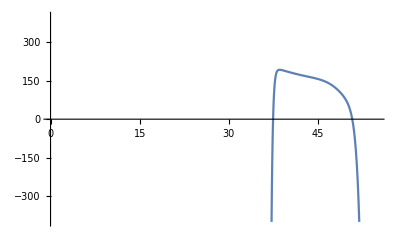

```mathematica
Plot[s1[[1]][[1]],{t,30,55},PlotRange->{{0,55},{-400,400}}]
```